```mathematica
allconditionsdir=SystemDialogInput["Directory"]
```

C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\

```mathematica
channelstable=Select[FileNames["*",allconditionsdir],DirectoryQ]
```

{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2}

```mathematica
ktspairstable=Table[Select[FileNames["*",channelstable[[i]]],DirectoryQ],{i,Length[channelstable]}]
```

{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21}}

```mathematica
todir=Function[dir,Select[FileNames["*",dir],DirectoryQ]]
```

Function[dir,Select[FileNames[*,dir],DirectoryQ]]

```mathematica
ktdirs=Map[todir,ktspairstable]
```

{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\11,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\13,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\22,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\17,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\3,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\12,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\20,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\28,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\31,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\2,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\4,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\21,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\6},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\11,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\13,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\22,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\17,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\3,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\12,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\20,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\28,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\31,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\2,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\4,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\21,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\6}}

```mathematica
endselect[list_,end_]:=Select[list,StringEndsQ[#,end]&];
```

```mathematica
(*Map[If[endselect[#,"newXY"]=={},{},endselect[#,"newXY"][[-1]]]&,Map[todir,Map[endselect[#,"(+-1)"]&,Map[Flatten[#]&,Map[todir,ktdirs,{5}],{4}],{4}],{5}],{5}]*)
```

```mathematica
ktdirsdatadir=Map[If[endselect[#,"newXYnew"]=={},{},endselect[#,"newXYnew"][[-1]]]&,Map[todir,Map[endselect[#,"(+-1)"]&,Map[Flatten[#]&,Map[todir,ktdirs,{5}],{4}],{4}],{5}],{5}]
```

{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\11,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\13,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\22,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\17,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\3,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\12,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\20,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\28,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\31,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\2,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\4,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\21,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\6},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\11,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\13,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\22,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\17,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\3,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\12,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\20,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\28,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\31,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\2,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\4,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\21,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\6}}

```mathematica
ktdirsdatadirdir=Map[If[(todir[#])=={},{},(todir[#])[[-1]]]<>"\\newMethod"&,ktdirsdatadir,{5}]
```

{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\11,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\13,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\22,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\17,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\3,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\12,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\20,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\28,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\31,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\2,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\4,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\21,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\6},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\11,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\13,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\22,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\17,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\3,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\12,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\20,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\28,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\31,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\2,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\4,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\21,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\6}}

```mathematica
(*ktdatapaths=Map[endselect[FileNames["*",#],".csv"][[1]]&,ktdirsdatadirdir,{5}];
*)
```

```mathematica
ktdatapaths=Map[If[endselect[FileNames["*",#],".csv"]=={},{},endselect[FileNames["*",#],".csv"][[1]]]&,ktdirsdatadirdir,{5}]
```

{{{{{D:\combine0802\control\d1c1control0707 done\ch1\15.-28\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\15.-28_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\d1c1control0707 done\ch1\15.-28\Path from Track_28 to Track_28.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\15.-28_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\d1c1control0707 done\ch1\16.-13\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\16.-13_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\d1c1control0707 done\ch1\16.-13\Path from Track_16 to Track_16.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\16.-13_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\d1c1control0707 done\ch1\18.-10\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\18.-10_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\d1c1control0707 done\ch1\18.-10\Path from Track_18 to Track_18.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\18.-10_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\d1c1control0707 done\ch1\3.-1\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\3.-1_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\d1c1control0707 done\ch1\3.-1\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\3.-1_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\d1c1control0707 done\ch1\5.-7\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\5.-7_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\d1c1control0707 done\ch1\5.-7\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\5.-7_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\control\d1c1control0707 done\ch2\15.-28\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\15.-28_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\d1c1control0707 done\ch2\15.-28\Path from Track_28 to Track_28.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\15.-28_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\d1c1control0707 done\ch2\16.-13\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\16.-13_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\d1c1control0707 done\ch2\16.-13\Path from Track_16 to Track_16.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\16.-13_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\d1c1control0707 done\ch2\18.-10\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\18.-10_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\d1c1control0707 done\ch2\18.-10\Path from Track_18 to Track_18.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\18.-10_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\d1c1control0707 done\ch2\3.-1\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\3.-1_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\d1c1control0707 done\ch2\3.-1\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\3.-1_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\d1c1control0707 done\ch2\5.-7\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\5.-7_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\d1c1control0707 done\ch2\5.-7\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\5.-7_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\control\dic1(0714\ch1\13.-20\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\13.-20_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\dic1(0714\ch1\13.-20\Path from Track_20 to Track_20.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\13.-20_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\dic1(0714\ch1\14.-23\Path from Track_14 to Track_14.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\14.-23_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\dic1(0714\ch1\14.-23\Path from Track_23 to Track_23.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\14.-23_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\dic1(0714\ch1\2.-19\Path from Track_19 to Track_19.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\2.-19_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\dic1(0714\ch1\2.-19\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\2.-19_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\dic1(0714\ch1\5.-10\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\5.-10_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\dic1(0714\ch1\5.-10\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\5.-10_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\dic1(0714\ch1\6.-11\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\6.-11_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\dic1(0714\ch1\6.-11\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\6.-11_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\control\dic1(0714\ch2\13.-20\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\13.-20_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\dic1(0714\ch2\13.-20\Path from Track_20 to Track_20.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\13.-20_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\dic1(0714\ch2\14.-23\Path from Track_14 to Track_14.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\14.-23_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\dic1(0714\ch2\14.-23\Path from Track_23 to Track_23.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\14.-23_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\dic1(0714\ch2\2.-19\Path from Track_19 to Track_19.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\2.-19_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\dic1(0714\ch2\2.-19\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\2.-19_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\dic1(0714\ch2\5.-10\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\5.-10_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\dic1(0714\ch2\5.-10\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\5.-10_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\dic1(0714\ch2\6.-11\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\6.-11_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\dic1(0714\ch2\6.-11\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\6.-11_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\control\new\ch1\0.-7\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\0.-7_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new\ch1\0.-7\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\0.-7_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new\ch1\1.-16\Path from Track_16 to Track_16.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\1.-16_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new\ch1\1.-16\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\1.-16_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new\ch1\9.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\9.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new\ch1\9.-6\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 8}, Day]0908resultXYnew\newMethod\9.-6_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\control\new\ch2\0.-7\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\0.-7_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new\ch2\0.-7\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\0.-7_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new\ch2\1.-16\Path from Track_16 to Track_16.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-16_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new\ch2\1.-16\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-16_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new\ch2\9.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\9.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new\ch2\9.-6\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\9.-6_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\control\new(2)(1)\ch1\13.-10\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-10_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1)\ch1\13.-10\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-10_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1)\ch1\14.-3\Path from Track_14 to Track_14.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\14.-3_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1)\ch1\14.-3\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\14.-3_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1)\ch1\2.-11\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\2.-11_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1)\ch1\2.-11\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\2.-11_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1)\ch1\5.-1\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\5.-1_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1)\ch1\5.-1\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\5.-1_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1)\ch1\7.-20\Path from Track_20 to Track_20.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-20_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1)\ch1\7.-20\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-20_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1)\ch1\8.-15\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-15_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1)\ch1\8.-15\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-15_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\control\new(2)(1)\ch2\13.-10\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-10_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1)\ch2\13.-10\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-10_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1)\ch2\14.-3\Path from Track_14 to Track_14.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\14.-3_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1)\ch2\14.-3\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\14.-3_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1)\ch2\2.-11\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\2.-11_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1)\ch2\2.-11\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\2.-11_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1)\ch2\5.-1\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\5.-1_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1)\ch2\5.-1\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\5.-1_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1)\ch2\7.-20\Path from Track_20 to Track_20.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-20_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1)\ch2\7.-20\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-20_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1)\ch2\8.-15\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-15_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1)\ch2\8.-15\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-15_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\control\new(2)(1) -new\ch1\12.-11\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\12.-11_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1) -new\ch1\12.-11\Path from Track_12 to Track_12.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\12.-11_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1) -new\ch1\1.-3\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-3_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1) -new\ch1\1.-3\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-3_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1) -new\ch1\13.-7\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-7_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1) -new\ch1\14.-10\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\14.-10_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1) -new\ch1\14.-10\Path from Track_14 to Track_14.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\14.-10_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1) -new\ch1\15.-9\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-9_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1) -new\ch1\15.-9\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-9_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1) -new\ch1\6.-4\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\6.-4_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1) -new\ch1\6.-4\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\6.-4_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\control\new(2)(1) -new\ch2\12.-11\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\12.-11_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1) -new\ch2\12.-11\Path from Track_12 to Track_12.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\12.-11_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1) -new\ch2\1.-3\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-3_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1) -new\ch2\1.-3\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-3_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1) -new\ch2\13.-7\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-7_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1) -new\ch2\13.-7\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-7_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1) -new\ch2\14.-10\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\14.-10_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1) -new\ch2\14.-10\Path from Track_14 to Track_14.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\14.-10_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1) -new\ch2\15.-9\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-9_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1) -new\ch2\15.-9\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-9_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(2)(1) -new\ch2\6.-4\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\6.-4_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(2)(1) -new\ch2\6.-4\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\6.-4_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\control\new(3)\ch1\0.-8\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\0.-8_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(3)\ch1\0.-8\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\0.-8_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(3)\ch1\10.-2\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(3)\ch1\11.-1\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\11.-1_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(3)\ch1\11.-1\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\11.-1_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(3)\ch1\5.-7\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\5.-7_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(3)\ch1\5.-7\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\5.-7_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\control\new(3)\ch2\0.-8\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\0.-8_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(3)\ch2\0.-8\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\0.-8_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(3)\ch2\10.-2\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(3)\ch2\10.-2\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(3)\ch2\11.-1\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\11.-1_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(3)\ch2\11.-1\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\11.-1_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(3)\ch2\5.-7\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\5.-7_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(3)\ch2\5.-7\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\5.-7_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\control\new(3)(1) - new\ch1\1.-5\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-5_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(3)(1) - new\ch1\1.-5\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-5_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(3)(1) - new\ch1\9.-0\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\9.-0_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(3)(1) - new\ch1\9.-0\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\9.-0_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\control\new(3)(1) - new\ch2\1.-5\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-5_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(3)(1) - new\ch2\1.-5\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-5_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\control\new(3)(1) - new\ch2\9.-0\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\9.-0_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\control\new(3)(1) - new\ch2\9.-0\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\9.-0_(+-1)_NewResult_0908XYnew.csv}}},{{{},{},{},{}},{{},{},{},{}}}},{{{{D:\combine0802\tsa\d3c1\ch1\10.-11\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-11_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c1\ch1\10.-11\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-11_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c1\ch1\1.-13\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-13_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c1\ch1\1.-13\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-13_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c1\ch1\4.-0\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\4.-0_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c1\ch1\4.-0\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\4.-0_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c1\ch1\7.-3\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-3_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c1\ch1\7.-3\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-3_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c1\ch1\8.-12\Path from Track_12 to Track_12.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-12_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c1\ch1\8.-12\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-12_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c1\ch1\9.-16\Path from Track_16 to Track_16.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\9.-16_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c1\ch1\9.-16\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\9.-16_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\tsa\d3c1\ch2\10.-11\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-11_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c1\ch2\10.-11\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-11_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c1\ch2\1.-13\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-13_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c1\ch2\1.-13\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-13_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c1\ch2\4.-0\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\4.-0_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c1\ch2\4.-0\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\4.-0_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c1\ch2\7.-3\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-3_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c1\ch2\7.-3\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-3_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c1\ch2\8.-12\Path from Track_12 to Track_12.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-12_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c1\ch2\8.-12\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-12_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c1\ch2\9.-16\Path from Track_16 to Track_16.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\9.-16_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c1\ch2\9.-16\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\9.-16_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\tsa\d3c2\ch1\1.-11\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-11_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c2\ch1\1.-11\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-11_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c2\ch1\12.-5\Path from Track_12 to Track_12.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\12.-5_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c2\ch1\12.-5\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\12.-5_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c2\ch1\15.-6\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c2\ch1\15.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-6_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c2\ch1\7.-3\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-3_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c2\ch1\7.-3\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-3_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\tsa\d3c2\ch2\1.-11\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-11_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c2\ch2\1.-11\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\1.-11_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c2\ch2\12.-5\Path from Track_12 to Track_12.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\12.-5_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c2\ch2\12.-5\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\12.-5_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c2\ch2\15.-6\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c2\ch2\15.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-6_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\d3c2\ch2\7.-3\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-3_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\d3c2\ch2\7.-3\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-3_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\tsa\new\ch1\10.-2\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new\ch1\10.-2\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new\ch1\12.-9\Path from Track_12 to Track_12.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\12.-9_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new\ch1\12.-9\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\12.-9_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new\ch1\7.-13\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-13_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new\ch1\7.-13\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-13_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new\ch1\8.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new\ch1\8.-6\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-6_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\tsa\new\ch2\10.-2\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new\ch2\10.-2\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new\ch2\12.-9\Path from Track_12 to Track_12.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\12.-9_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new\ch2\12.-9\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\12.-9_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new\ch2\7.-13\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-13_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new\ch2\7.-13\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-13_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new\ch2\8.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new\ch2\8.-6\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-6_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\tsa\new (2)\ch1\10.-1\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-1_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (2)\ch1\10.-1\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-1_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (2)\ch1\2.-15\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\2.-15_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (2)\ch1\2.-15\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\2.-15_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (2)\ch1\4.-11\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\4.-11_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (2)\ch1\4.-11\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\4.-11_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (2)\ch1\8.-14\Path from Track_14 to Track_14.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-14_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (2)\ch1\8.-14\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-14_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\tsa\new (2)\ch2\10.-1\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-1_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (2)\ch2\10.-1\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-1_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (2)\ch2\2.-15\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\2.-15_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (2)\ch2\2.-15\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\2.-15_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (2)\ch2\4.-11\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\4.-11_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (2)\ch2\4.-11\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\4.-11_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (2)\ch2\8.-14\Path from Track_14 to Track_14.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-14_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (2)\ch2\8.-14\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-14_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\tsa\new (3)\ch1\13.-0\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-0_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (3)\ch1\13.-0\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-0_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (3)\ch1\15.-2\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-2_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (3)\ch1\15.-2\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-2_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (3)\ch1\7.-3\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-3_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (3)\ch1\7.-3\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-3_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\tsa\new (3)\ch2\13.-0\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-0_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (3)\ch2\13.-0\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-0_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (3)\ch2\15.-2\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-2_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (3)\ch2\7.-3\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-3_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (3)\ch2\7.-3\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-3_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\tsa\new (5)\ch1\14.-3\Path from Track_14 to Track_14.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\14.-3_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (5)\ch1\14.-3\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\14.-3_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (5)\ch1\15.-12\Path from Track_12 to Track_12.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-12_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (5)\ch1\15.-12\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-12_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (5)\ch1\16.-6\Path from Track_16 to Track_16.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\16.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (5)\ch1\16.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\16.-6_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (5)\ch1\7.-10\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-10_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (5)\ch1\7.-10\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-10_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (5)\ch1\8.-4\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-4_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (5)\ch1\8.-4\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-4_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\tsa\new (5)\ch2\14.-3\Path from Track_14 to Track_14.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\14.-3_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (5)\ch2\14.-3\Path from Track_3 to Track_3.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\14.-3_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (5)\ch2\15.-12\Path from Track_12 to Track_12.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-12_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (5)\ch2\15.-12\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-12_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (5)\ch2\16.-6\Path from Track_16 to Track_16.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\16.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (5)\ch2\16.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\16.-6_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (5)\ch2\7.-10\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-10_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (5)\ch2\7.-10\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\7.-10_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\new (5)\ch2\8.-4\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-4_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\new (5)\ch2\8.-4\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\8.-4_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\tsa\newfolder(2,1)\ch1\10.-2\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1)\ch1\10.-2\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1)\ch1\11.-14\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\11.-14_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1)\ch1\11.-14\Path from Track_14 to Track_14.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\11.-14_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1)\ch1\13.-6\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\13.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1)\ch1\13.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\13.-6_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1)\ch1\7.-15\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\7.-15_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1)\ch1\7.-15\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\7.-15_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1)\ch1\8.-4\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\8.-4_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1)\ch1\8.-4\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\8.-4_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\tsa\newfolder(2,1)\ch2\10.-2\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1)\ch2\10.-2\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1)\ch2\11.-14\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\11.-14_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1)\ch2\11.-14\Path from Track_14 to Track_14.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\11.-14_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1)\ch2\13.-6\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\13.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1)\ch2\13.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\13.-6_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1)\ch2\7.-15\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\7.-15_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1)\ch2\7.-15\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\7.-15_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1)\ch2\8.-4\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\8.-4_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1)\ch2\8.-4\Path from Track_8 to Track_8.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\8.-4_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\tsa\newfolder(2,1) - new\ch1\11.-0\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\11.-0_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new\ch1\11.-0\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\11.-0_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch1\17.-5\Path from Track_17 to Track_17.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\17.-5_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new\ch1\17.-5\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\17.-5_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch1\18.-6\Path from Track_18 to Track_18.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\18.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new\ch1\18.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\18.-6_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch1\4.-15\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\4.-15_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new\ch1\4.-15\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\4.-15_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch1\9.-13\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\9.-13_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new\ch1\9.-13\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\9.-13_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\tsa\newfolder(2,1) - new\ch2\11.-0\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\11.-0_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new\ch2\11.-0\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\11.-0_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch2\17.-5\Path from Track_17 to Track_17.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\17.-5_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new\ch2\17.-5\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\17.-5_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch2\18.-6\Path from Track_18 to Track_18.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\18.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new\ch2\18.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\18.-6_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch2\4.-15\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\4.-15_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new\ch2\4.-15\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\4.-15_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch2\9.-13\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\9.-13_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new\ch2\9.-13\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\9.-13_(+-1)_NewResult_0908XYnew.csv}}},{{{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\0.-1\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\0.-1_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\0.-1\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\0.-1_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\10.-9\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\10.-9_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\10.-9\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\10.-9_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\11.-5\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\11.-5_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\11.-5\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\11.-5_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\12.-13\Path from Track_12 to Track_12.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\12.-13_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\12.-13\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\12.-13_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\4.-6\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\4.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\4.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\4.-6_(+-1)_NewResult_0908XYnew.csv}},{{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\0.-1\Path from Track_0 to Track_0.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\0.-1_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\0.-1\Path from Track_1 to Track_1.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\0.-1_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\10.-9\Path from Track_10 to Track_10.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\10.-9_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\10.-9\Path from Track_9 to Track_9.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\10.-9_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\11.-5\Path from Track_11 to Track_11.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\11.-5_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\11.-5\Path from Track_5 to Track_5.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\11.-5_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\12.-13\Path from Track_12 to Track_12.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\12.-13_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\12.-13\Path from Track_13 to Track_13.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\12.-13_(+-1)_NewResult_0908XYnew.csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\4.-6\Path from Track_4 to Track_4.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\4.-6_(+-1)_NewResult_0908XYnew.csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\4.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\4.-6_(+-1)_NewResult_0908XYnew.csv}}}}}

```mathematica
tokk=Function[dir,Select[FileNames["*",dir],StringContainsQ[#,"(number)kkDistanceWithFramesNumberOnly"]&]]
```

Function[dir,Select[FileNames[*,dir],StringContainsQ[#1,(number)kkDistanceWithFramesNumberOnly]&]]

```mathematica
kkdirs=Map[{tokk[#][[1]],tokk[#][[1]]}&,ktspairstable,{4}]
```

{{{{{D:\combine0802\control\d1c1control0707 done\ch1\15.-28\(number)kkDistanceWithFramesNumberOnly15.-28..csv,D:\combine0802\control\d1c1control0707 done\ch1\15.-28\(number)kkDistanceWithFramesNumberOnly15.-28..csv},{D:\combine0802\control\d1c1control0707 done\ch1\16.-13\(number)kkDistanceWithFramesNumberOnly16.-13..csv,D:\combine0802\control\d1c1control0707 done\ch1\16.-13\(number)kkDistanceWithFramesNumberOnly16.-13..csv},{D:\combine0802\control\d1c1control0707 done\ch1\18.-10\(number)kkDistanceWithFramesNumberOnly18.-10..csv,D:\combine0802\control\d1c1control0707 done\ch1\18.-10\(number)kkDistanceWithFramesNumberOnly18.-10..csv},{D:\combine0802\control\d1c1control0707 done\ch1\3.-1\(number)kkDistanceWithFramesNumberOnly3.-1..csv,D:\combine0802\control\d1c1control0707 done\ch1\3.-1\(number)kkDistanceWithFramesNumberOnly3.-1..csv},{D:\combine0802\control\d1c1control0707 done\ch1\5.-7\(number)kkDistanceWithFramesNumberOnly5.-7..csv,D:\combine0802\control\d1c1control0707 done\ch1\5.-7\(number)kkDistanceWithFramesNumberOnly5.-7..csv}},{{D:\combine0802\control\d1c1control0707 done\ch2\15.-28\(number)kkDistanceWithFramesNumberOnly15.-28..csv,D:\combine0802\control\d1c1control0707 done\ch2\15.-28\(number)kkDistanceWithFramesNumberOnly15.-28..csv},{D:\combine0802\control\d1c1control0707 done\ch2\16.-13\(number)kkDistanceWithFramesNumberOnly16.-13..csv,D:\combine0802\control\d1c1control0707 done\ch2\16.-13\(number)kkDistanceWithFramesNumberOnly16.-13..csv},{D:\combine0802\control\d1c1control0707 done\ch2\18.-10\(number)kkDistanceWithFramesNumberOnly18.-10..csv,D:\combine0802\control\d1c1control0707 done\ch2\18.-10\(number)kkDistanceWithFramesNumberOnly18.-10..csv},{D:\combine0802\control\d1c1control0707 done\ch2\3.-1\(number)kkDistanceWithFramesNumberOnly3.-1..csv,D:\combine0802\control\d1c1control0707 done\ch2\3.-1\(number)kkDistanceWithFramesNumberOnly3.-1..csv},{D:\combine0802\control\d1c1control0707 done\ch2\5.-7\(number)kkDistanceWithFramesNumberOnly5.-7..csv,D:\combine0802\control\d1c1control0707 done\ch2\5.-7\(number)kkDistanceWithFramesNumberOnly5.-7..csv}}},{{{D:\combine0802\control\dic1(0714\ch1\13.-20\(number)kkDistanceWithFramesNumberOnly13.-20..csv,D:\combine0802\control\dic1(0714\ch1\13.-20\(number)kkDistanceWithFramesNumberOnly13.-20..csv},{D:\combine0802\control\dic1(0714\ch1\14.-23\(number)kkDistanceWithFramesNumberOnly14.-23..csv,D:\combine0802\control\dic1(0714\ch1\14.-23\(number)kkDistanceWithFramesNumberOnly14.-23..csv},{D:\combine0802\control\dic1(0714\ch1\2.-19\(number)kkDistanceWithFramesNumberOnly2.-19..csv,D:\combine0802\control\dic1(0714\ch1\2.-19\(number)kkDistanceWithFramesNumberOnly2.-19..csv},{D:\combine0802\control\dic1(0714\ch1\5.-10\(number)kkDistanceWithFramesNumberOnly5.-10..csv,D:\combine0802\control\dic1(0714\ch1\5.-10\(number)kkDistanceWithFramesNumberOnly5.-10..csv},{D:\combine0802\control\dic1(0714\ch1\6.-11\(number)kkDistanceWithFramesNumberOnly6.-11..csv,D:\combine0802\control\dic1(0714\ch1\6.-11\(number)kkDistanceWithFramesNumberOnly6.-11..csv}},{{D:\combine0802\control\dic1(0714\ch2\13.-20\(number)kkDistanceWithFramesNumberOnly13.-20..csv,D:\combine0802\control\dic1(0714\ch2\13.-20\(number)kkDistanceWithFramesNumberOnly13.-20..csv},{D:\combine0802\control\dic1(0714\ch2\14.-23\(number)kkDistanceWithFramesNumberOnly14.-23..csv,D:\combine0802\control\dic1(0714\ch2\14.-23\(number)kkDistanceWithFramesNumberOnly14.-23..csv},{D:\combine0802\control\dic1(0714\ch2\2.-19\(number)kkDistanceWithFramesNumberOnly2.-19..csv,D:\combine0802\control\dic1(0714\ch2\2.-19\(number)kkDistanceWithFramesNumberOnly2.-19..csv},{D:\combine0802\control\dic1(0714\ch2\5.-10\(number)kkDistanceWithFramesNumberOnly5.-10..csv,D:\combine0802\control\dic1(0714\ch2\5.-10\(number)kkDistanceWithFramesNumberOnly5.-10..csv},{D:\combine0802\control\dic1(0714\ch2\6.-11\(number)kkDistanceWithFramesNumberOnly6.-11..csv,D:\combine0802\control\dic1(0714\ch2\6.-11\(number)kkDistanceWithFramesNumberOnly6.-11..csv}}},{{{D:\combine0802\control\new\ch1\0.-7\(number)kkDistanceWithFramesNumberOnly0.-7..csv,D:\combine0802\control\new\ch1\0.-7\(number)kkDistanceWithFramesNumberOnly0.-7..csv},{D:\combine0802\control\new\ch1\1.-16\(number)kkDistanceWithFramesNumberOnly1.-16..csv,D:\combine0802\control\new\ch1\1.-16\(number)kkDistanceWithFramesNumberOnly1.-16..csv},{D:\combine0802\control\new\ch1\9.-6\(number)kkDistanceWithFramesNumberOnly9.-6..csv,D:\combine0802\control\new\ch1\9.-6\(number)kkDistanceWithFramesNumberOnly9.-6..csv}},{{D:\combine0802\control\new\ch2\0.-7\(number)kkDistanceWithFramesNumberOnly0.-7..csv,D:\combine0802\control\new\ch2\0.-7\(number)kkDistanceWithFramesNumberOnly0.-7..csv},{D:\combine0802\control\new\ch2\1.-16\(number)kkDistanceWithFramesNumberOnly1.-16..csv,D:\combine0802\control\new\ch2\1.-16\(number)kkDistanceWithFramesNumberOnly1.-16..csv},{D:\combine0802\control\new\ch2\9.-6\(number)kkDistanceWithFramesNumberOnly9.-6..csv,D:\combine0802\control\new\ch2\9.-6\(number)kkDistanceWithFramesNumberOnly9.-6..csv}}},{{{D:\combine0802\control\new(2)(1)\ch1\13.-10\(number)kkDistanceWithFramesNumberOnly13.-10..csv,D:\combine0802\control\new(2)(1)\ch1\13.-10\(number)kkDistanceWithFramesNumberOnly13.-10..csv},{D:\combine0802\control\new(2)(1)\ch1\14.-3\(number)kkDistanceWithFramesNumberOnly14.-3..csv,D:\combine0802\control\new(2)(1)\ch1\14.-3\(number)kkDistanceWithFramesNumberOnly14.-3..csv},{D:\combine0802\control\new(2)(1)\ch1\2.-11\(number)kkDistanceWithFramesNumberOnly2.-11..csv,D:\combine0802\control\new(2)(1)\ch1\2.-11\(number)kkDistanceWithFramesNumberOnly2.-11..csv},{D:\combine0802\control\new(2)(1)\ch1\5.-1\(number)kkDistanceWithFramesNumberOnly5.-1..csv,D:\combine0802\control\new(2)(1)\ch1\5.-1\(number)kkDistanceWithFramesNumberOnly5.-1..csv},{D:\combine0802\control\new(2)(1)\ch1\7.-20\(number)kkDistanceWithFramesNumberOnly7.-20..csv,D:\combine0802\control\new(2)(1)\ch1\7.-20\(number)kkDistanceWithFramesNumberOnly7.-20..csv},{D:\combine0802\control\new(2)(1)\ch1\8.-15\(number)kkDistanceWithFramesNumberOnly8.-15..csv,D:\combine0802\control\new(2)(1)\ch1\8.-15\(number)kkDistanceWithFramesNumberOnly8.-15..csv}},{{D:\combine0802\control\new(2)(1)\ch2\13.-10\(number)kkDistanceWithFramesNumberOnly13.-10..csv,D:\combine0802\control\new(2)(1)\ch2\13.-10\(number)kkDistanceWithFramesNumberOnly13.-10..csv},{D:\combine0802\control\new(2)(1)\ch2\14.-3\(number)kkDistanceWithFramesNumberOnly14.-3..csv,D:\combine0802\control\new(2)(1)\ch2\14.-3\(number)kkDistanceWithFramesNumberOnly14.-3..csv},{D:\combine0802\control\new(2)(1)\ch2\2.-11\(number)kkDistanceWithFramesNumberOnly2.-11..csv,D:\combine0802\control\new(2)(1)\ch2\2.-11\(number)kkDistanceWithFramesNumberOnly2.-11..csv},{D:\combine0802\control\new(2)(1)\ch2\5.-1\(number)kkDistanceWithFramesNumberOnly5.-1..csv,D:\combine0802\control\new(2)(1)\ch2\5.-1\(number)kkDistanceWithFramesNumberOnly5.-1..csv},{D:\combine0802\control\new(2)(1)\ch2\7.-20\(number)kkDistanceWithFramesNumberOnly7.-20..csv,D:\combine0802\control\new(2)(1)\ch2\7.-20\(number)kkDistanceWithFramesNumberOnly7.-20..csv},{D:\combine0802\control\new(2)(1)\ch2\8.-15\(number)kkDistanceWithFramesNumberOnly8.-15..csv,D:\combine0802\control\new(2)(1)\ch2\8.-15\(number)kkDistanceWithFramesNumberOnly8.-15..csv}}},{{{D:\combine0802\control\new(2)(1) -new\ch1\12.-11\(number)kkDistanceWithFramesNumberOnly12.-11..csv,D:\combine0802\control\new(2)(1) -new\ch1\12.-11\(number)kkDistanceWithFramesNumberOnly12.-11..csv},{D:\combine0802\control\new(2)(1) -new\ch1\1.-3\(number)kkDistanceWithFramesNumberOnly1.-3..csv,D:\combine0802\control\new(2)(1) -new\ch1\1.-3\(number)kkDistanceWithFramesNumberOnly1.-3..csv},{D:\combine0802\control\new(2)(1) -new\ch1\13.-7\(number)kkDistanceWithFramesNumberOnly13.-7..csv,D:\combine0802\control\new(2)(1) -new\ch1\13.-7\(number)kkDistanceWithFramesNumberOnly13.-7..csv},{D:\combine0802\control\new(2)(1) -new\ch1\14.-10\(number)kkDistanceWithFramesNumberOnly14.-10..csv,D:\combine0802\control\new(2)(1) -new\ch1\14.-10\(number)kkDistanceWithFramesNumberOnly14.-10..csv},{D:\combine0802\control\new(2)(1) -new\ch1\15.-9\(number)kkDistanceWithFramesNumberOnly15.-9..csv,D:\combine0802\control\new(2)(1) -new\ch1\15.-9\(number)kkDistanceWithFramesNumberOnly15.-9..csv},{D:\combine0802\control\new(2)(1) -new\ch1\6.-4\(number)kkDistanceWithFramesNumberOnly6.-4..csv,D:\combine0802\control\new(2)(1) -new\ch1\6.-4\(number)kkDistanceWithFramesNumberOnly6.-4..csv}},{{D:\combine0802\control\new(2)(1) -new\ch2\12.-11\(number)kkDistanceWithFramesNumberOnly12.-11..csv,D:\combine0802\control\new(2)(1) -new\ch2\12.-11\(number)kkDistanceWithFramesNumberOnly12.-11..csv},{D:\combine0802\control\new(2)(1) -new\ch2\1.-3\(number)kkDistanceWithFramesNumberOnly1.-3..csv,D:\combine0802\control\new(2)(1) -new\ch2\1.-3\(number)kkDistanceWithFramesNumberOnly1.-3..csv},{D:\combine0802\control\new(2)(1) -new\ch2\13.-7\(number)kkDistanceWithFramesNumberOnly13.-7..csv,D:\combine0802\control\new(2)(1) -new\ch2\13.-7\(number)kkDistanceWithFramesNumberOnly13.-7..csv},{D:\combine0802\control\new(2)(1) -new\ch2\14.-10\(number)kkDistanceWithFramesNumberOnly14.-10..csv,D:\combine0802\control\new(2)(1) -new\ch2\14.-10\(number)kkDistanceWithFramesNumberOnly14.-10..csv},{D:\combine0802\control\new(2)(1) -new\ch2\15.-9\(number)kkDistanceWithFramesNumberOnly15.-9..csv,D:\combine0802\control\new(2)(1) -new\ch2\15.-9\(number)kkDistanceWithFramesNumberOnly15.-9..csv},{D:\combine0802\control\new(2)(1) -new\ch2\6.-4\(number)kkDistanceWithFramesNumberOnly6.-4..csv,D:\combine0802\control\new(2)(1) -new\ch2\6.-4\(number)kkDistanceWithFramesNumberOnly6.-4..csv}}},{{{D:\combine0802\control\new(3)\ch1\0.-8\(number)kkDistanceWithFramesNumberOnly0.-8..csv,D:\combine0802\control\new(3)\ch1\0.-8\(number)kkDistanceWithFramesNumberOnly0.-8..csv},{D:\combine0802\control\new(3)\ch1\10.-2\(number)kkDistanceWithFramesNumberOnly10.-2..csv,D:\combine0802\control\new(3)\ch1\10.-2\(number)kkDistanceWithFramesNumberOnly10.-2..csv},{D:\combine0802\control\new(3)\ch1\11.-1\(number)kkDistanceWithFramesNumberOnly11.-1..csv,D:\combine0802\control\new(3)\ch1\11.-1\(number)kkDistanceWithFramesNumberOnly11.-1..csv},{D:\combine0802\control\new(3)\ch1\5.-7\(number)kkDistanceWithFramesNumberOnly5.-7..csv,D:\combine0802\control\new(3)\ch1\5.-7\(number)kkDistanceWithFramesNumberOnly5.-7..csv}},{{D:\combine0802\control\new(3)\ch2\0.-8\(number)kkDistanceWithFramesNumberOnly0.-8..csv,D:\combine0802\control\new(3)\ch2\0.-8\(number)kkDistanceWithFramesNumberOnly0.-8..csv},{D:\combine0802\control\new(3)\ch2\10.-2\(number)kkDistanceWithFramesNumberOnly10.-2..csv,D:\combine0802\control\new(3)\ch2\10.-2\(number)kkDistanceWithFramesNumberOnly10.-2..csv},{D:\combine0802\control\new(3)\ch2\11.-1\(number)kkDistanceWithFramesNumberOnly11.-1..csv,D:\combine0802\control\new(3)\ch2\11.-1\(number)kkDistanceWithFramesNumberOnly11.-1..csv},{D:\combine0802\control\new(3)\ch2\5.-7\(number)kkDistanceWithFramesNumberOnly5.-7..csv,D:\combine0802\control\new(3)\ch2\5.-7\(number)kkDistanceWithFramesNumberOnly5.-7..csv}}},{{{D:\combine0802\control\new(3)(1) - new\ch1\1.-5\(number)kkDistanceWithFramesNumberOnly1.-5..csv,D:\combine0802\control\new(3)(1) - new\ch1\1.-5\(number)kkDistanceWithFramesNumberOnly1.-5..csv},{D:\combine0802\control\new(3)(1) - new\ch1\9.-0\(number)kkDistanceWithFramesNumberOnly9.-0..csv,D:\combine0802\control\new(3)(1) - new\ch1\9.-0\(number)kkDistanceWithFramesNumberOnly9.-0..csv}},{{D:\combine0802\control\new(3)(1) - new\ch2\1.-5\(number)kkDistanceWithFramesNumberOnly1.-5..csv,D:\combine0802\control\new(3)(1) - new\ch2\1.-5\(number)kkDistanceWithFramesNumberOnly1.-5..csv},{D:\combine0802\control\new(3)(1) - new\ch2\9.-0\(number)kkDistanceWithFramesNumberOnly9.-0..csv,D:\combine0802\control\new(3)(1) - new\ch2\9.-0\(number)kkDistanceWithFramesNumberOnly9.-0..csv}}},{{{D:\combine0802\control\new(4)(1) - new\ch1\1.-11\(number)kkDistanceWithFramesNumberOnly1.-11..csv,D:\combine0802\control\new(4)(1) - new\ch1\1.-11\(number)kkDistanceWithFramesNumberOnly1.-11..csv},{D:\combine0802\control\new(4)(1) - new\ch1\2.-8\(number)kkDistanceWithFramesNumberOnly2.-8..csv,D:\combine0802\control\new(4)(1) - new\ch1\2.-8\(number)kkDistanceWithFramesNumberOnly2.-8..csv},{D:\combine0802\control\new(4)(1) - new\ch1\6.-3\(number)kkDistanceWithFramesNumberOnly6.-3..csv,D:\combine0802\control\new(4)(1) - new\ch1\6.-3\(number)kkDistanceWithFramesNumberOnly6.-3..csv},{D:\combine0802\control\new(4)(1) - new\ch1\9.-0\(number)kkDistanceWithFramesNumberOnly9.-0..csv,D:\combine0802\control\new(4)(1) - new\ch1\9.-0\(number)kkDistanceWithFramesNumberOnly9.-0..csv}},{{D:\combine0802\control\new(4)(1) - new\ch2\1.-11\(number)kkDistanceWithFramesNumberOnly1.-11..csv,D:\combine0802\control\new(4)(1) - new\ch2\1.-11\(number)kkDistanceWithFramesNumberOnly1.-11..csv},{D:\combine0802\control\new(4)(1) - new\ch2\2.-8\(number)kkDistanceWithFramesNumberOnly2.-8..csv,D:\combine0802\control\new(4)(1) - new\ch2\2.-8\(number)kkDistanceWithFramesNumberOnly2.-8..csv},{D:\combine0802\control\new(4)(1) - new\ch2\6.-3\(number)kkDistanceWithFramesNumberOnly6.-3..csv,D:\combine0802\control\new(4)(1) - new\ch2\6.-3\(number)kkDistanceWithFramesNumberOnly6.-3..csv},{D:\combine0802\control\new(4)(1) - new\ch2\9.-0\(number)kkDistanceWithFramesNumberOnly9.-0..csv,D:\combine0802\control\new(4)(1) - new\ch2\9.-0\(number)kkDistanceWithFramesNumberOnly9.-0..csv}}}},{{{{D:\combine0802\tsa\d3c1\ch1\10.-11\(number)kkDistanceWithFramesNumberOnly10.-11..csv,D:\combine0802\tsa\d3c1\ch1\10.-11\(number)kkDistanceWithFramesNumberOnly10.-11..csv},{D:\combine0802\tsa\d3c1\ch1\1.-13\(number)kkDistanceWithFramesNumberOnly1.-13..csv,D:\combine0802\tsa\d3c1\ch1\1.-13\(number)kkDistanceWithFramesNumberOnly1.-13..csv},{D:\combine0802\tsa\d3c1\ch1\4.-0\(number)kkDistanceWithFramesNumberOnly4.-0..csv,D:\combine0802\tsa\d3c1\ch1\4.-0\(number)kkDistanceWithFramesNumberOnly4.-0..csv},{D:\combine0802\tsa\d3c1\ch1\7.-3\(number)kkDistanceWithFramesNumberOnly7.-3..csv,D:\combine0802\tsa\d3c1\ch1\7.-3\(number)kkDistanceWithFramesNumberOnly7.-3..csv},{D:\combine0802\tsa\d3c1\ch1\8.-12\(number)kkDistanceWithFramesNumberOnly8.-12..csv,D:\combine0802\tsa\d3c1\ch1\8.-12\(number)kkDistanceWithFramesNumberOnly8.-12..csv},{D:\combine0802\tsa\d3c1\ch1\9.-16\(number)kkDistanceWithFramesNumberOnly9.-16..csv,D:\combine0802\tsa\d3c1\ch1\9.-16\(number)kkDistanceWithFramesNumberOnly9.-16..csv}},{{D:\combine0802\tsa\d3c1\ch2\10.-11\(number)kkDistanceWithFramesNumberOnly10.-11..csv,D:\combine0802\tsa\d3c1\ch2\10.-11\(number)kkDistanceWithFramesNumberOnly10.-11..csv},{D:\combine0802\tsa\d3c1\ch2\1.-13\(number)kkDistanceWithFramesNumberOnly1.-13..csv,D:\combine0802\tsa\d3c1\ch2\1.-13\(number)kkDistanceWithFramesNumberOnly1.-13..csv},{D:\combine0802\tsa\d3c1\ch2\4.-0\(number)kkDistanceWithFramesNumberOnly4.-0..csv,D:\combine0802\tsa\d3c1\ch2\4.-0\(number)kkDistanceWithFramesNumberOnly4.-0..csv},{D:\combine0802\tsa\d3c1\ch2\7.-3\(number)kkDistanceWithFramesNumberOnly7.-3..csv,D:\combine0802\tsa\d3c1\ch2\7.-3\(number)kkDistanceWithFramesNumberOnly7.-3..csv},{D:\combine0802\tsa\d3c1\ch2\8.-12\(number)kkDistanceWithFramesNumberOnly8.-12..csv,D:\combine0802\tsa\d3c1\ch2\8.-12\(number)kkDistanceWithFramesNumberOnly8.-12..csv},{D:\combine0802\tsa\d3c1\ch2\9.-16\(number)kkDistanceWithFramesNumberOnly9.-16..csv,D:\combine0802\tsa\d3c1\ch2\9.-16\(number)kkDistanceWithFramesNumberOnly9.-16..csv}}},{{{D:\combine0802\tsa\d3c2\ch1\1.-11\(number)kkDistanceWithFramesNumberOnly1.-11..csv,D:\combine0802\tsa\d3c2\ch1\1.-11\(number)kkDistanceWithFramesNumberOnly1.-11..csv},{D:\combine0802\tsa\d3c2\ch1\12.-5\(number)kkDistanceWithFramesNumberOnly12.-5..csv,D:\combine0802\tsa\d3c2\ch1\12.-5\(number)kkDistanceWithFramesNumberOnly12.-5..csv},{D:\combine0802\tsa\d3c2\ch1\15.-6\(number)kkDistanceWithFramesNumberOnly15.-6..csv,D:\combine0802\tsa\d3c2\ch1\15.-6\(number)kkDistanceWithFramesNumberOnly15.-6..csv},{D:\combine0802\tsa\d3c2\ch1\7.-3\(number)kkDistanceWithFramesNumberOnly7.-3..csv,D:\combine0802\tsa\d3c2\ch1\7.-3\(number)kkDistanceWithFramesNumberOnly7.-3..csv}},{{D:\combine0802\tsa\d3c2\ch2\1.-11\(number)kkDistanceWithFramesNumberOnly1.-11..csv,D:\combine0802\tsa\d3c2\ch2\1.-11\(number)kkDistanceWithFramesNumberOnly1.-11..csv},{D:\combine0802\tsa\d3c2\ch2\12.-5\(number)kkDistanceWithFramesNumberOnly12.-5..csv,D:\combine0802\tsa\d3c2\ch2\12.-5\(number)kkDistanceWithFramesNumberOnly12.-5..csv},{D:\combine0802\tsa\d3c2\ch2\15.-6\(number)kkDistanceWithFramesNumberOnly15.-6..csv,D:\combine0802\tsa\d3c2\ch2\15.-6\(number)kkDistanceWithFramesNumberOnly15.-6..csv},{D:\combine0802\tsa\d3c2\ch2\7.-3\(number)kkDistanceWithFramesNumberOnly7.-3..csv,D:\combine0802\tsa\d3c2\ch2\7.-3\(number)kkDistanceWithFramesNumberOnly7.-3..csv}}},{{{D:\combine0802\tsa\new\ch1\10.-2\(number)kkDistanceWithFramesNumberOnly10.-2..csv,D:\combine0802\tsa\new\ch1\10.-2\(number)kkDistanceWithFramesNumberOnly10.-2..csv},{D:\combine0802\tsa\new\ch1\12.-9\(number)kkDistanceWithFramesNumberOnly12.-9..csv,D:\combine0802\tsa\new\ch1\12.-9\(number)kkDistanceWithFramesNumberOnly12.-9..csv},{D:\combine0802\tsa\new\ch1\7.-13\(number)kkDistanceWithFramesNumberOnly7.-13..csv,D:\combine0802\tsa\new\ch1\7.-13\(number)kkDistanceWithFramesNumberOnly7.-13..csv},{D:\combine0802\tsa\new\ch1\8.-6\(number)kkDistanceWithFramesNumberOnly8.-6..csv,D:\combine0802\tsa\new\ch1\8.-6\(number)kkDistanceWithFramesNumberOnly8.-6..csv}},{{D:\combine0802\tsa\new\ch2\10.-2\(number)kkDistanceWithFramesNumberOnly10.-2..csv,D:\combine0802\tsa\new\ch2\10.-2\(number)kkDistanceWithFramesNumberOnly10.-2..csv},{D:\combine0802\tsa\new\ch2\12.-9\(number)kkDistanceWithFramesNumberOnly12.-9..csv,D:\combine0802\tsa\new\ch2\12.-9\(number)kkDistanceWithFramesNumberOnly12.-9..csv},{D:\combine0802\tsa\new\ch2\7.-13\(number)kkDistanceWithFramesNumberOnly7.-13..csv,D:\combine0802\tsa\new\ch2\7.-13\(number)kkDistanceWithFramesNumberOnly7.-13..csv},{D:\combine0802\tsa\new\ch2\8.-6\(number)kkDistanceWithFramesNumberOnly8.-6..csv,D:\combine0802\tsa\new\ch2\8.-6\(number)kkDistanceWithFramesNumberOnly8.-6..csv}}},{{{D:\combine0802\tsa\new (2)\ch1\10.-1\(number)kkDistanceWithFramesNumberOnly10.-1..csv,D:\combine0802\tsa\new (2)\ch1\10.-1\(number)kkDistanceWithFramesNumberOnly10.-1..csv},{D:\combine0802\tsa\new (2)\ch1\2.-15\(number)kkDistanceWithFramesNumberOnly2.-15..csv,D:\combine0802\tsa\new (2)\ch1\2.-15\(number)kkDistanceWithFramesNumberOnly2.-15..csv},{D:\combine0802\tsa\new (2)\ch1\4.-11\(number)kkDistanceWithFramesNumberOnly4.-11..csv,D:\combine0802\tsa\new (2)\ch1\4.-11\(number)kkDistanceWithFramesNumberOnly4.-11..csv},{D:\combine0802\tsa\new (2)\ch1\8.-14\(number)kkDistanceWithFramesNumberOnly8.-14..csv,D:\combine0802\tsa\new (2)\ch1\8.-14\(number)kkDistanceWithFramesNumberOnly8.-14..csv}},{{D:\combine0802\tsa\new (2)\ch2\10.-1\(number)kkDistanceWithFramesNumberOnly10.-1..csv,D:\combine0802\tsa\new (2)\ch2\10.-1\(number)kkDistanceWithFramesNumberOnly10.-1..csv},{D:\combine0802\tsa\new (2)\ch2\2.-15\(number)kkDistanceWithFramesNumberOnly2.-15..csv,D:\combine0802\tsa\new (2)\ch2\2.-15\(number)kkDistanceWithFramesNumberOnly2.-15..csv},{D:\combine0802\tsa\new (2)\ch2\4.-11\(number)kkDistanceWithFramesNumberOnly4.-11..csv,D:\combine0802\tsa\new (2)\ch2\4.-11\(number)kkDistanceWithFramesNumberOnly4.-11..csv},{D:\combine0802\tsa\new (2)\ch2\8.-14\(number)kkDistanceWithFramesNumberOnly8.-14..csv,D:\combine0802\tsa\new (2)\ch2\8.-14\(number)kkDistanceWithFramesNumberOnly8.-14..csv}}},{{{D:\combine0802\tsa\new (3)\ch1\13.-0\(number)kkDistanceWithFramesNumberOnly13.-0..csv,D:\combine0802\tsa\new (3)\ch1\13.-0\(number)kkDistanceWithFramesNumberOnly13.-0..csv},{D:\combine0802\tsa\new (3)\ch1\15.-2\(number)kkDistanceWithFramesNumberOnly15.-2..csv,D:\combine0802\tsa\new (3)\ch1\15.-2\(number)kkDistanceWithFramesNumberOnly15.-2..csv},{D:\combine0802\tsa\new (3)\ch1\7.-3\(number)kkDistanceWithFramesNumberOnly7.-3..csv,D:\combine0802\tsa\new (3)\ch1\7.-3\(number)kkDistanceWithFramesNumberOnly7.-3..csv}},{{D:\combine0802\tsa\new (3)\ch2\13.-0\(number)kkDistanceWithFramesNumberOnly13.-0..csv,D:\combine0802\tsa\new (3)\ch2\13.-0\(number)kkDistanceWithFramesNumberOnly13.-0..csv},{D:\combine0802\tsa\new (3)\ch2\15.-2\(number)kkDistanceWithFramesNumberOnly15.-2..csv,D:\combine0802\tsa\new (3)\ch2\15.-2\(number)kkDistanceWithFramesNumberOnly15.-2..csv},{D:\combine0802\tsa\new (3)\ch2\7.-3\(number)kkDistanceWithFramesNumberOnly7.-3..csv,D:\combine0802\tsa\new (3)\ch2\7.-3\(number)kkDistanceWithFramesNumberOnly7.-3..csv}}},{{{D:\combine0802\tsa\new (5)\ch1\14.-3\(number)kkDistanceWithFramesNumberOnly14.-3..csv,D:\combine0802\tsa\new (5)\ch1\14.-3\(number)kkDistanceWithFramesNumberOnly14.-3..csv},{D:\combine0802\tsa\new (5)\ch1\15.-12\(number)kkDistanceWithFramesNumberOnly15.-12..csv,D:\combine0802\tsa\new (5)\ch1\15.-12\(number)kkDistanceWithFramesNumberOnly15.-12..csv},{D:\combine0802\tsa\new (5)\ch1\16.-6\(number)kkDistanceWithFramesNumberOnly16.-6..csv,D:\combine0802\tsa\new (5)\ch1\16.-6\(number)kkDistanceWithFramesNumberOnly16.-6..csv},{D:\combine0802\tsa\new (5)\ch1\7.-10\(number)kkDistanceWithFramesNumberOnly7.-10..csv,D:\combine0802\tsa\new (5)\ch1\7.-10\(number)kkDistanceWithFramesNumberOnly7.-10..csv},{D:\combine0802\tsa\new (5)\ch1\8.-4\(number)kkDistanceWithFramesNumberOnly8.-4..csv,D:\combine0802\tsa\new (5)\ch1\8.-4\(number)kkDistanceWithFramesNumberOnly8.-4..csv}},{{D:\combine0802\tsa\new (5)\ch2\14.-3\(number)kkDistanceWithFramesNumberOnly14.-3..csv,D:\combine0802\tsa\new (5)\ch2\14.-3\(number)kkDistanceWithFramesNumberOnly14.-3..csv},{D:\combine0802\tsa\new (5)\ch2\15.-12\(number)kkDistanceWithFramesNumberOnly15.-12..csv,D:\combine0802\tsa\new (5)\ch2\15.-12\(number)kkDistanceWithFramesNumberOnly15.-12..csv},{D:\combine0802\tsa\new (5)\ch2\16.-6\(number)kkDistanceWithFramesNumberOnly16.-6..csv,D:\combine0802\tsa\new (5)\ch2\16.-6\(number)kkDistanceWithFramesNumberOnly16.-6..csv},{D:\combine0802\tsa\new (5)\ch2\7.-10\(number)kkDistanceWithFramesNumberOnly7.-10..csv,D:\combine0802\tsa\new (5)\ch2\7.-10\(number)kkDistanceWithFramesNumberOnly7.-10..csv},{D:\combine0802\tsa\new (5)\ch2\8.-4\(number)kkDistanceWithFramesNumberOnly8.-4..csv,D:\combine0802\tsa\new (5)\ch2\8.-4\(number)kkDistanceWithFramesNumberOnly8.-4..csv}}},{{{D:\combine0802\tsa\newfolder(2,1)\ch1\10.-2\(number)kkDistanceWithFramesNumberOnly10.-2..csv,D:\combine0802\tsa\newfolder(2,1)\ch1\10.-2\(number)kkDistanceWithFramesNumberOnly10.-2..csv},{D:\combine0802\tsa\newfolder(2,1)\ch1\11.-14\(number)kkDistanceWithFramesNumberOnly11.-14..csv,D:\combine0802\tsa\newfolder(2,1)\ch1\11.-14\(number)kkDistanceWithFramesNumberOnly11.-14..csv},{D:\combine0802\tsa\newfolder(2,1)\ch1\13.-6\(number)kkDistanceWithFramesNumberOnly13.-6..csv,D:\combine0802\tsa\newfolder(2,1)\ch1\13.-6\(number)kkDistanceWithFramesNumberOnly13.-6..csv},{D:\combine0802\tsa\newfolder(2,1)\ch1\7.-15\(number)kkDistanceWithFramesNumberOnly7.-15..csv,D:\combine0802\tsa\newfolder(2,1)\ch1\7.-15\(number)kkDistanceWithFramesNumberOnly7.-15..csv},{D:\combine0802\tsa\newfolder(2,1)\ch1\8.-4\(number)kkDistanceWithFramesNumberOnly8.-4..csv,D:\combine0802\tsa\newfolder(2,1)\ch1\8.-4\(number)kkDistanceWithFramesNumberOnly8.-4..csv}},{{D:\combine0802\tsa\newfolder(2,1)\ch2\10.-2\(number)kkDistanceWithFramesNumberOnly10.-2..csv,D:\combine0802\tsa\newfolder(2,1)\ch2\10.-2\(number)kkDistanceWithFramesNumberOnly10.-2..csv},{D:\combine0802\tsa\newfolder(2,1)\ch2\11.-14\(number)kkDistanceWithFramesNumberOnly11.-14..csv,D:\combine0802\tsa\newfolder(2,1)\ch2\11.-14\(number)kkDistanceWithFramesNumberOnly11.-14..csv},{D:\combine0802\tsa\newfolder(2,1)\ch2\13.-6\(number)kkDistanceWithFramesNumberOnly13.-6..csv,D:\combine0802\tsa\newfolder(2,1)\ch2\13.-6\(number)kkDistanceWithFramesNumberOnly13.-6..csv},{D:\combine0802\tsa\newfolder(2,1)\ch2\7.-15\(number)kkDistanceWithFramesNumberOnly7.-15..csv,D:\combine0802\tsa\newfolder(2,1)\ch2\7.-15\(number)kkDistanceWithFramesNumberOnly7.-15..csv},{D:\combine0802\tsa\newfolder(2,1)\ch2\8.-4\(number)kkDistanceWithFramesNumberOnly8.-4..csv,D:\combine0802\tsa\newfolder(2,1)\ch2\8.-4\(number)kkDistanceWithFramesNumberOnly8.-4..csv}}},{{{D:\combine0802\tsa\newfolder(2,1) - new\ch1\11.-0\(number)kkDistanceWithFramesNumberOnly11.-0..csv,D:\combine0802\tsa\newfolder(2,1) - new\ch1\11.-0\(number)kkDistanceWithFramesNumberOnly11.-0..csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch1\17.-5\(number)kkDistanceWithFramesNumberOnly17.-5..csv,D:\combine0802\tsa\newfolder(2,1) - new\ch1\17.-5\(number)kkDistanceWithFramesNumberOnly17.-5..csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch1\18.-6\(number)kkDistanceWithFramesNumberOnly18.-6..csv,D:\combine0802\tsa\newfolder(2,1) - new\ch1\18.-6\(number)kkDistanceWithFramesNumberOnly18.-6..csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch1\4.-15\(number)kkDistanceWithFramesNumberOnly4.-15..csv,D:\combine0802\tsa\newfolder(2,1) - new\ch1\4.-15\(number)kkDistanceWithFramesNumberOnly4.-15..csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch1\9.-13\(number)kkDistanceWithFramesNumberOnly9.-13..csv,D:\combine0802\tsa\newfolder(2,1) - new\ch1\9.-13\(number)kkDistanceWithFramesNumberOnly9.-13..csv}},{{D:\combine0802\tsa\newfolder(2,1) - new\ch2\11.-0\(number)kkDistanceWithFramesNumberOnly11.-0..csv,D:\combine0802\tsa\newfolder(2,1) - new\ch2\11.-0\(number)kkDistanceWithFramesNumberOnly11.-0..csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch2\17.-5\(number)kkDistanceWithFramesNumberOnly17.-5..csv,D:\combine0802\tsa\newfolder(2,1) - new\ch2\17.-5\(number)kkDistanceWithFramesNumberOnly17.-5..csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch2\18.-6\(number)kkDistanceWithFramesNumberOnly18.-6..csv,D:\combine0802\tsa\newfolder(2,1) - new\ch2\18.-6\(number)kkDistanceWithFramesNumberOnly18.-6..csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch2\4.-15\(number)kkDistanceWithFramesNumberOnly4.-15..csv,D:\combine0802\tsa\newfolder(2,1) - new\ch2\4.-15\(number)kkDistanceWithFramesNumberOnly4.-15..csv},{D:\combine0802\tsa\newfolder(2,1) - new\ch2\9.-13\(number)kkDistanceWithFramesNumberOnly9.-13..csv,D:\combine0802\tsa\newfolder(2,1) - new\ch2\9.-13\(number)kkDistanceWithFramesNumberOnly9.-13..csv}}},{{{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\0.-1\(number)kkDistanceWithFramesNumberOnly0.-1..csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\0.-1\(number)kkDistanceWithFramesNumberOnly0.-1..csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\10.-9\(number)kkDistanceWithFramesNumberOnly10.-9..csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\10.-9\(number)kkDistanceWithFramesNumberOnly10.-9..csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\11.-5\(number)kkDistanceWithFramesNumberOnly11.-5..csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\11.-5\(number)kkDistanceWithFramesNumberOnly11.-5..csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\12.-13\(number)kkDistanceWithFramesNumberOnly12.-13..csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\12.-13\(number)kkDistanceWithFramesNumberOnly12.-13..csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\4.-6\(number)kkDistanceWithFramesNumberOnly4.-6..csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\4.-6\(number)kkDistanceWithFramesNumberOnly4.-6..csv}},{{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\0.-1\(number)kkDistanceWithFramesNumberOnly0.-1..csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\0.-1\(number)kkDistanceWithFramesNumberOnly0.-1..csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\10.-9\(number)kkDistanceWithFramesNumberOnly10.-9..csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\10.-9\(number)kkDistanceWithFramesNumberOnly10.-9..csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\11.-5\(number)kkDistanceWithFramesNumberOnly11.-5..csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\11.-5\(number)kkDistanceWithFramesNumberOnly11.-5..csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\12.-13\(number)kkDistanceWithFramesNumberOnly12.-13..csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\12.-13\(number)kkDistanceWithFramesNumberOnly12.-13..csv},{D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\4.-6\(number)kkDistanceWithFramesNumberOnly4.-6..csv,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch2\4.-6\(number)kkDistanceWithFramesNumberOnly4.-6..csv}}}}}

```mathematica
kkdata=Map[Transpose[Import[#]][[1]]&,kkdirs,{5}]
```

{{{{1},{{{2.04273,1.66619,1.39221,1.48346,1.65855,2.20992,2.66959,3.128,40,2.61675,2.16542,2.04273,1.96674,2.05718,2.14776,2.25541,2.54459},{1}},3,{{1},1}}},6,{1}},1}
 |  |  |  |

```mathematica
lis25[list_]:=Length[list]==10
```

```mathematica
havedata[list_]:=NumberQ[list[[3]]]&&NumberQ[list[[4]]]&&NumberQ[list[[5]]]
```

```mathematica
n=m=l=j=i=t=2
```

2

```mathematica
(*Join[{n,m,l,j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[l]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]][[1]]]]}],{"//",n,m,conjugate[l],j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[conjugate[l]]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]][[1]]]]}]]*)
```

```mathematica
conjugate[x_]:=If[x==1,2,1]
```

```mathematica
(*Select[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]],!lis25[#]&]*)
```

```mathematica
(*Length[Select[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]],!lis25[#]&]]==0*)
```

```mathematica
(*StringQ[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]&&StringQ[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]&&Length[Select[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]],!lis25[#]&]]==0&&Length[Select[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]],!lis25[#]&]]==0*)
```

```mathematica
(*If[StringQ[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]&&StringQ[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]](*&&*)(*Length[Select[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]],!lis25[#]&]]==0&&*)(*Length[Select[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]],!lis25[#]&]]==0*),Table[If[havedata[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]&&Length[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]]>=t&&havedata[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]]],Join[{n,m,l,j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[l]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]][[1]]]]}],{"//",n,m,conjugate[l],j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[conjugate[l]]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]][[1]]]]}]]],{t,Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]]}]]*)
```

```mathematica
ktXYdatatest44export=Table[Table[Table[Table[Table[If[StringQ[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]&&StringQ[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]&&Length[Select[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]],!lis25[#]&]]==0&&Length[Select[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]],!lis25[#]&]]==0,Table[If[havedata[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]&&Length[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]]>=t&&havedata[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]]],Join[{n,m,l,j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[l]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]][[1]]]]}],{"//",n,m,conjugate[l],j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[conjugate[l]]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]][[1]]]]}]]],{t,Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]]}]],{i,Length[ktdatapaths[[n]][[m]][[l]][[j]]]}],{j,Length[ktdatapaths[[n]][[m]][[l]]]}],{l,Length[ktdatapaths[[n]][[m]]]}],{m,Length[ktdatapaths[[n]]]}],{n,Length[ktdatapaths]}]
```

Part::partw: Part 2 of {D:\combine0802\control\new(2)(1) -new\ch1\13.-7\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-7_(+-1)_NewResult_0908XYnew.csv} does not exist.

Part::partw: Part 2 of {D:\combine0802\control\new(3)\ch1\10.-2\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv} does not exist.

Part::partw: Part 2 of {D:\combine0802\tsa\new (3)\ch2\15.-2\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-2_(+-1)_NewResult_0908XYnew.csv} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1},{{{1},{1}},1,{{1},{1}},3,{{1},{{{Null,17,{2,7,2,1,1,19,/,18,True,19,0.220199,0.208295,-2.82731,0.0704094,0.929591,False,,0.046*"",2.23846}},Null},3,{1}}},{{1},{1}},{{1},{1}}}}
 |  |  |  |

```mathematica
(*ktmeandwidthdataflatten44export=Map[Flatten[#,1]&,Map[Transpose[#]&,Map[Flatten[#,1]&,ktmeandwidthdatatest44export,{3}],{1}],{2}]*)
```

```mathematica
ktXYflatten44export={Flatten[ktXYdatatest44export[[1]],4],Flatten[ktXYdatatest44export[[2]],4]}
```

{{Null,{1,1,1,1,1,2,/,1,True,0.255452,0.282648,-2.33917,0.339096,0.660904,False,,0.046*"",2.04273,//,1,1,2,1,1,2,/,1,True,0.234781,0.268901,-2.33008,0.343544,0.656456,False,,0.046*"",2.04273},5013,Null},{Null,6259,{1}}}
 |  |  |  |

```mathematica
(*ktmeandwidthdataflatten44export=Flatten[ktmeandwidthdatatest44export,5]*)
```

```mathematica
Export["controlXYnew0904.csv",Select[ktXYflatten44export[[1]],ListQ[#]&&#[[3]]==1&]]
```

controlXYnew0904.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["controlXYnew0904.csv"]]]
```

```mathematica
Export["TSAXYnew0904.csv",Select[ktXYflatten44export[[2]],ListQ[#]&&#[[3]]==1&]]
```

TSAXYnew0904.csv

```mathematica
SystemOpen["TSAXYnew0904.csv"]
```

```mathematica
controlXY=Import["controlXYnew0904.csv"];
```

```mathematica
tsaXY=Import["TSAXYnew0904.csv"];
```

```mathematica
"{x,y,angle}"
```

{x,y,angle}

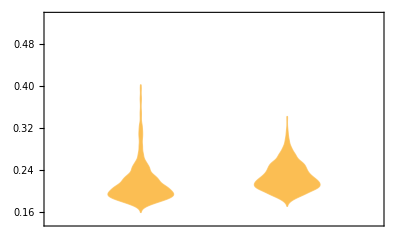

```mathematica
DistributionChart[{Transpose[controlXY][[10]],Transpose[controlXY][[11]]}]
```

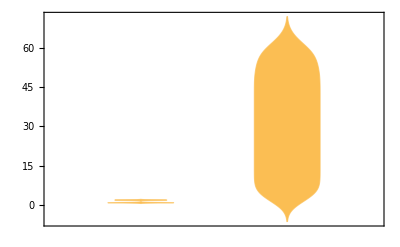

```mathematica
DistributionChart[{Transpose[controlXY][[24]],Transpose[controlXY][[25]]}]
```

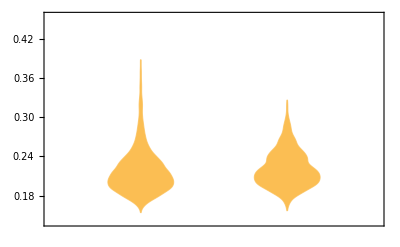

```mathematica
DistributionChart[{Transpose[tsaXY][[10]],Transpose[tsaXY][[11]]}]
```

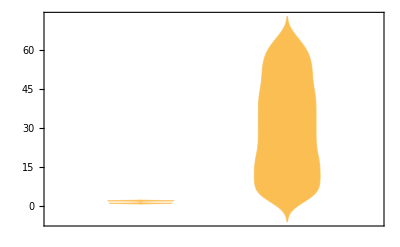

```mathematica
DistributionChart[{Transpose[tsaXY][[24]],Transpose[tsaXY][[25]]}]
```

```mathematica
Map[Mean,{Transpose[controlXY][[10]],Transpose[controlXY][[11]],Transpose[controlXY][[24]],Transpose[controlXY][[25]],Transpose[tsaXY][[10]],Transpose[tsaXY][[11]],Transpose[tsaXY][[24]],Transpose[tsaXY][[25]]}]
```

{0.216144,0.227045,271/188,76787/2444,0.218899,0.221186,4612/3049,94070/3049}

```mathematica
DistributionChart[{Transpose[controlXY][[10]],Transpose[controlXY][[11]]}]
```

-Graphics-

```mathematica
DistributionChart[{Transpose[controlXY][[24]],Transpose[controlXY][[25]]}]
```

-Graphics-

```mathematica
DistributionChart[{Transpose[tsaXY][[10]],Transpose[tsaXY][[11]]}]
```

-Graphics-

```mathematica
DistributionChart[{Transpose[tsaXY][[24]],Transpose[tsaXY][[25]]}]
```

-Graphics-

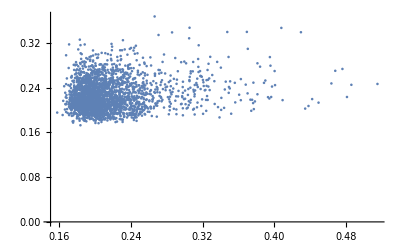

```mathematica
ListPlot[Transpose[{Transpose[controlXY][[10]],Transpose[controlXY][[11]]}],PlotRange->All]
```

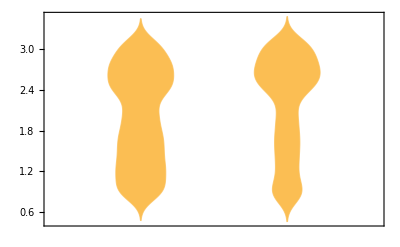

```mathematica
DistributionChart[Abs[{Transpose[controlXY][[12]],Transpose[controlXY][[31]]}]]
```

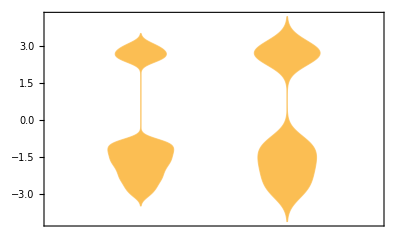

```mathematica
DistributionChart[{Transpose[controlXY][[12]],Transpose[controlXY][[31]]}]
```

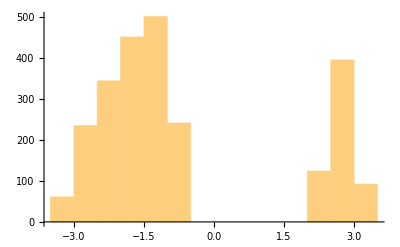

```mathematica
Histogram[Transpose[controlXY][[12]]]
```

```mathematica
anglecorrect[anglist_]:=Map[Which[Abs[#]<=Pi/2,#,#>Pi/2,Pi-#,#<-Pi/2,Pi+#]&,anglist]*180/Pi
```

```mathematica
absanglecorrect[anglist_]:=Abs[Map[Which[Abs[#]<=Pi/2,#,#>Pi/2,Pi-#,#<-Pi/2,Pi+#]&,anglist]*180/Pi]
```

```mathematica
[Abs[{Join[Pi-Abs[Transpose[controlXY][[12]]],Abs[Transpose[controlXY][[12]]]],Join[Abs[Transpose[controlXY][[26]]],Pi-Abs[Transpose[controlXY][[26]]]]}]]
```

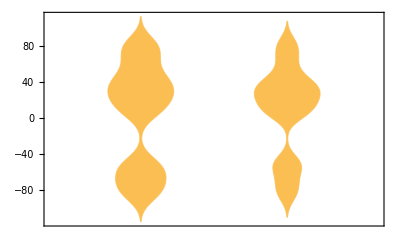

```mathematica
DistributionChart[{anglecorrect[Transpose[controlXY][[12]]],anglecorrect[Transpose[controlXY][[31]]]}]
```

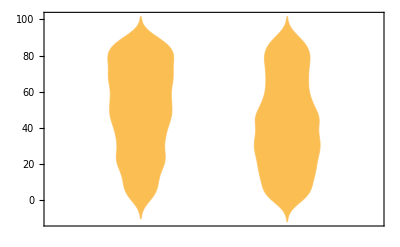

```mathematica
DistributionChart[{absanglecorrect[Transpose[controlXY][[12]]],absanglecorrect[Transpose[controlXY][[31]]]}]
```

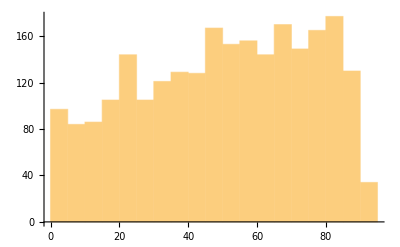

```mathematica
Histogram[absanglecorrect[Transpose[controlXY][[12]]]]
```

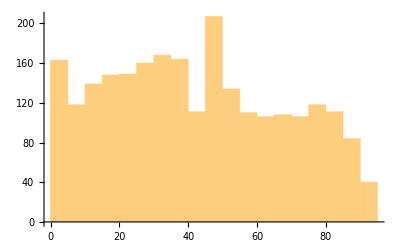

```mathematica
Histogram[absanglecorrect[Transpose[controlXY][[31]]]]
```

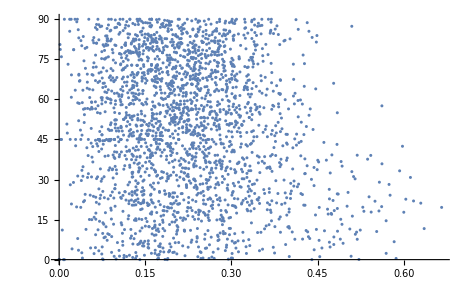

```mathematica
ListPlot[Transpose[{Transpose[controlXY][[13]],absanglecorrect[Transpose[controlXY][[12]]]}],PlotRange->All]
```

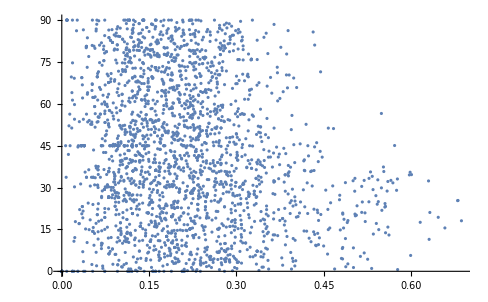

```mathematica
ListPlot[Transpose[{Transpose[controlXY][[32]],absanglecorrect[Transpose[controlXY][[31]]]}],PlotRange->All]
```

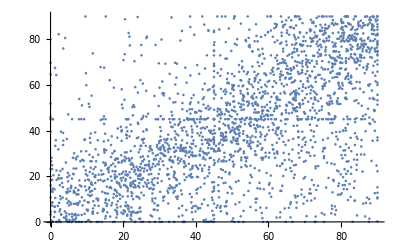

```mathematica
ListPlot[Transpose[{absanglecorrect[Transpose[controlXY][[12]]],absanglecorrect[Transpose[controlXY][[31]]]}],PlotRange->All]
```

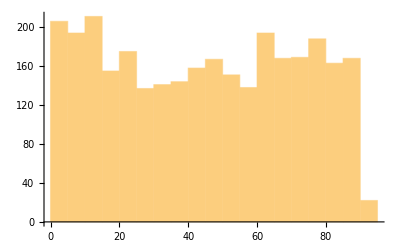

```mathematica
Histogram[absanglecorrect[Transpose[tsaXY][[12]]]]
```

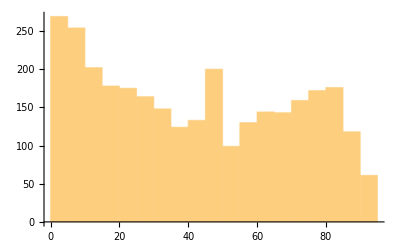

```mathematica
Histogram[absanglecorrect[Transpose[tsaXY][[31]]]]
```

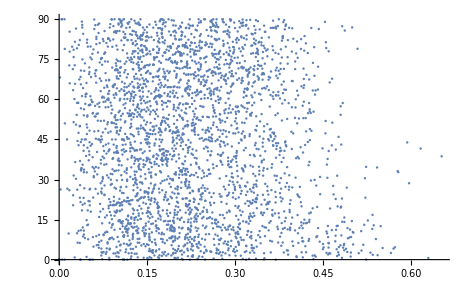

```mathematica
ListPlot[Transpose[{Transpose[tsaXY][[13]],absanglecorrect[Transpose[tsaXY][[12]]]}],PlotRange->All]
```

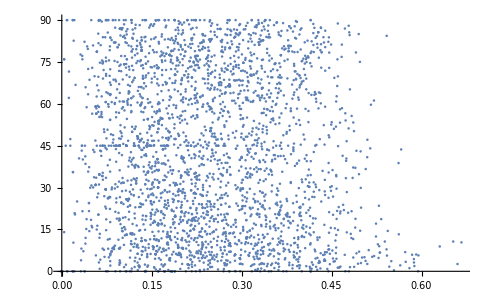

```mathematica
ListPlot[Transpose[{Transpose[tsaXY][[32]],absanglecorrect[Transpose[tsaXY][[31]]]}],PlotRange->All]
```

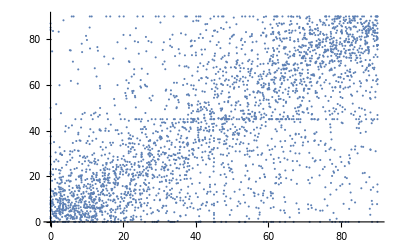

```mathematica
ListPlot[Transpose[{absanglecorrect[Transpose[tsaXY][[12]]],absanglecorrect[Transpose[tsaXY][[31]]]}],PlotRange->All]
```

```mathematica
Join[Transpose[{Abs[Transpose[controlXY][[12]]],Abs[Transpose[controlXY][[31]]]}],Transpose[{Pi-Abs[Transpose[controlXY][[12]]],Pi-Abs[Transpose[controlXY][[31]]]}]]
```

{{2.33917,2.33008},{2.37954,2.44448},{2.20857,2.36351},{2.19311,2.16403},{2.01912,2.14786},4878,{0.780054,2.11122},{0.785398,0.785398},{0.850504,0.785398},{1.31877,0.566015},{1.72115,0.36754}}
 |  |  |  |

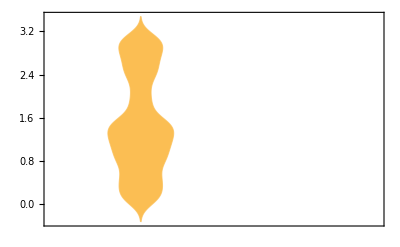

```mathematica
DistributionChart[Abs[{Join[Abs[Transpose[tsaXY][[12]]]-Pi/2,Abs[Transpose[tsaXY][[12]]]],Join[Abs[Transpose[tsaXY][[26]]],Abs[Transpose[tsaXY][[26]]]-Pi/2]}]]
```

```mathematica
Abs[Abs[{Join[Pi-Transpose[tsaXY][[12]],Transpose[tsaXY][[12]]],Join[Transpose[tsaXY][[26]],Pi-Transpose[tsaXY][[26]]]}]]
```

{{4.89953,4.86771,4.9397,4.90865,4.57403,4.28675,0.627763,4.73155,5.49288,4.67262,6078,2.47987,2.52834,2.29593,2.4925,2.37035,2.20782,3.04377,3.03408,2.77877,2.65287},{1}}
 |  |  |  |

```mathematica
tailcontrol1=Select[controlXY,#[[15]]=="True"&];
```

```mathematica
tailcontrol2=Select[controlXY,#[[34]]=="True"&];
```

```mathematica
tailtsa1=Select[tsaXY,#[[15]]=="True"&];
```

```mathematica
tailtsa2=Select[tsaXY,#[[34]]=="True"&];
```

```mathematica
taildirection[list_]:=Map[Which[#=="right",+1,#=="left",-1]&,list]
```

```mathematica
taildirection[Transpose[tailcontrol][[16]]]
```

{1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,-1,1,-1,-1,1,1,1,1,-1,1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

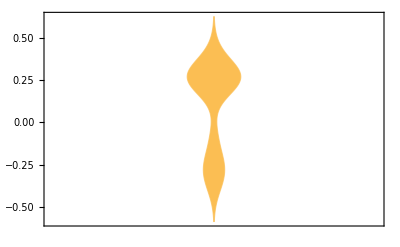

```mathematica
DistributionChart[{Transpose[tailcontrol1][[17]]*taildirection[Transpose[tailcontrol1][[16]]]}]
```

```mathematica
DistributionChart[{Transpose[tailcontrol2][[36]]*taildirection[Transpose[tailcontrol2][[35]]]}]
```

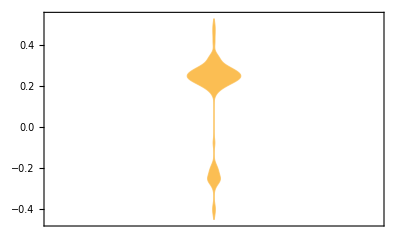

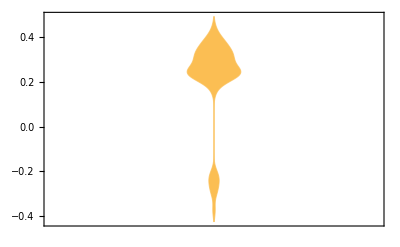

```mathematica
DistributionChart[{Transpose[tailtsa1][[36]]*taildirection[Transpose[tailtsa1][[35]]]}]
```

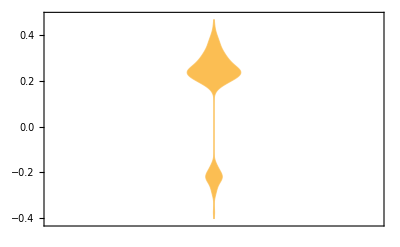

```mathematica
DistributionChart[{Transpose[tailtsa2][[36]]*taildirection[Transpose[tailtsa2][[35]]]}]
```

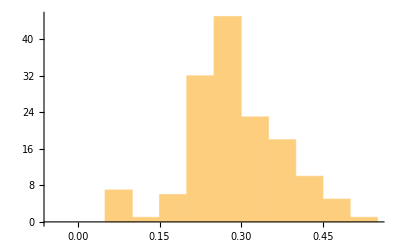

```mathematica
Histogram[Transpose[controlXY][[17]]]
```

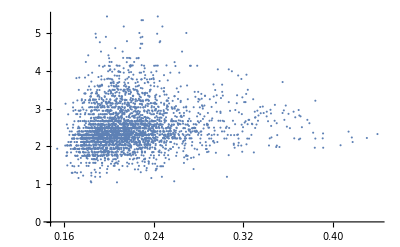

```mathematica
ListPlot[Transpose[{Transpose[tsaXY][[10]],Transpose[tsaXY][[18]]}],PlotRange->All]
```

```mathematica
ListPlot[Transpose[{Transpose[controlXY][[10]],Transpose[controlXY][[11]]}],PlotRange->All]
```

-Graphics-

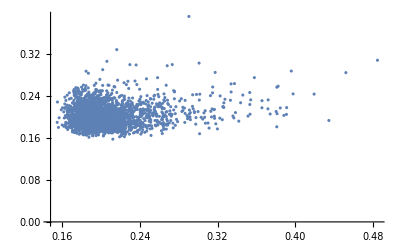

```mathematica
ListPlot[Transpose[{Transpose[controlXY][[29]],Transpose[controlXY][[30]]}],PlotRange->All]
```

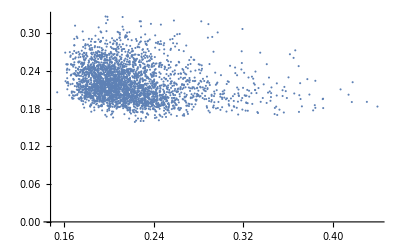

```mathematica
ListPlot[Transpose[{Transpose[tsaXY][[10]],Transpose[tsaXY][[11]]}],PlotRange->All]
```

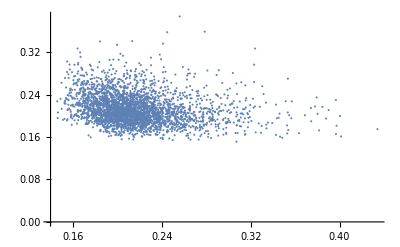

```mathematica
ListPlot[Transpose[{Transpose[tsaXY][[29]],Transpose[tsaXY][[30]]}],PlotRange->All]
```

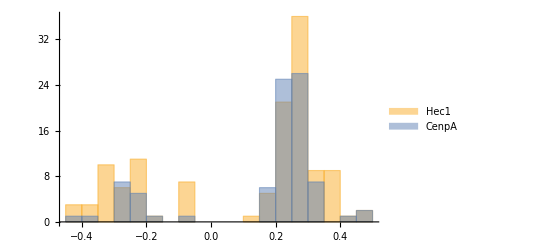

```mathematica
Histogram[{Transpose[tailcontrol1][[17]]*taildirection[Transpose[tailcontrol1][[16]]],Transpose[tailcontrol2][[36]]*taildirection[Transpose[tailcontrol2][[35]]]},20,PlotRange->All,ChartLegends->{Hec1, CenpA}]
```

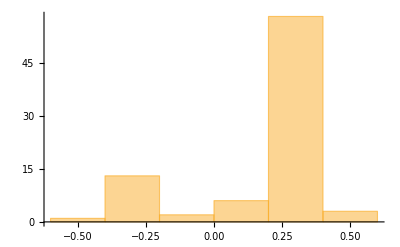

```mathematica
Histogram[{Transpose[tailcontrol2][[36]]*taildirection[Transpose[tailcontrol2][[35]]]},PlotRange->All]
```

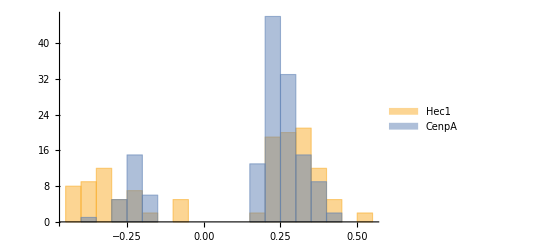

```mathematica
Histogram[{Transpose[tailtsa1][[17]]*taildirection[Transpose[tailtsa1][[16]]],Transpose[tailtsa2][[36]]*taildirection[Transpose[tailtsa2][[35]]]},20,PlotRange->All,ChartLegends->{Hec1, CenpA}]
```

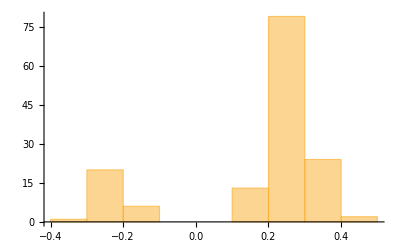

```mathematica
Histogram[{Transpose[tailtsa2][[36]]*taildirection[Transpose[tailtsa2][[35]]]},PlotRange->All]
```

```mathematica
ktXYdatatest44export2=Table[Table[Table[Table[Table[If[StringQ[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]&&StringQ[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]&&Length[Select[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]],!lis25[#]&]]==0&&Length[Select[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]],!lis25[#]&]]==0,Table[If[havedata[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]&&Length[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]]>=t&&havedata[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]]],Join[{n,m,l,j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]],{"//"},{kkdata[[n]][[m]][[l]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]][[1]]]]},{ktdatapaths[[n]][[m]][[l]][[j]][[i]]}],{"////",n,m,conjugate[l],j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]],{"//"},{kkdata[[n]][[m]][[conjugate[l]]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]][[1]]]]},{ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]}]]],{t,Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]]}]],{i,Length[ktdatapaths[[n]][[m]][[l]][[j]]]}],{j,Length[ktdatapaths[[n]][[m]][[l]]]}],{l,Length[ktdatapaths[[n]][[m]]]}],{m,Length[ktdatapaths[[n]]]}],{n,Length[ktdatapaths]}]
```

Part::partw: Part 2 of {D:\combine0802\control\new(2)(1) -new\ch1\13.-7\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-7_(+-1)_NewResult_0908XYnew.csv} does not exist.

Part::partw: Part 2 of {D:\combine0802\control\new(3)\ch1\10.-2\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv} does not exist.

Part::partw: Part 2 of {D:\combine0802\tsa\new (3)\ch2\15.-2\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-2_(+-1)_NewResult_0908XYnew.csv} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1},{1}}
 |  |  |  |

```mathematica
ktXYflatten44export2={Flatten[ktXYdatatest44export2[[1]],4],Flatten[ktXYdatatest44export2[[2]],4]}
```

{{Null,5014,Null},{Null,6259,{2,9,2,5,2,61,/,60,True,23,-2.65287,0.0879415,0.912059,False,,0.046*"",//,2.6054,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\4.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\4.-6_(+-1)_NewResult_0908XYnew.csv}}}
 |  |  |  |

```mathematica
Export["controlXYnew0907.csv",Select[ktXYflatten44export2[[1]],ListQ[#]&&#[[3]]==1&]]
```

controlXYnew0907.csv

```mathematica
Export["TSAXYnew0907.csv",Select[ktXYflatten44export2[[2]],ListQ[#]&&#[[3]]==1&]]
```

TSAXYnew0907.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["TSAXYnew0907.csv"]]]
```

```mathematica
controlXY0911=Import["controlXYnew0907.csv"];
```

```mathematica
tsaXY0911=Import["TSAXYnew0907.csv"];
```

```mathematica
tailcontrol1new=Select[controlXY0911,#[[15]]=="True"&];
```

```mathematica
tailcontrol2new=Select[controlXY0911,#[[34]]=="True"&];
```

```mathematica
tailtsa1new=Select[tsaXY0911,#[[15]]=="True"&];
```

```mathematica
tailtsa2new=Select[tsaXY0911,#[[34]]=="True"&];
```

```mathematica
taildirection[list_]:=Map[Which[#=="right",+1,#=="left",-1]&,list]
```

```mathematica
(*taildirection[Transpose[tailcontrol][[16]]]*)
```

Part::partw: Part 36 of {} does not exist.

Part::partw: Part 35 of {} does not exist.

Part::pkspec1: The expression Null cannot be used as a part specification.

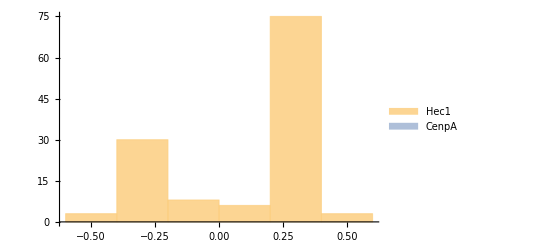

```mathematica
Histogram[{Transpose[tailcontrol1new][[17]]*taildirection[Transpose[tailcontrol1new][[16]]],Transpose[tailcontrol2new][[36]]*taildirection[Transpose[tailcontrol2new][[35]]]},PlotRange->All,ChartLegends->{Hec1, CenpA}]
```

Part::partw: Part 36 of {} does not exist.

Part::partw: Part 35 of {} does not exist.

Part::pkspec1: The expression Null cannot be used as a part specification.

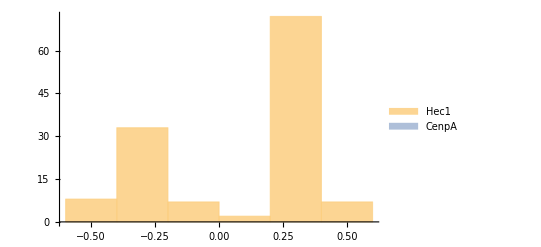

```mathematica
Histogram[{Transpose[tailtsa1new][[17]]*taildirection[Transpose[tailtsa1new][[16]]],Transpose[tailtsa2new][[36]]*taildirection[Transpose[tailtsa2new][[35]]]},PlotRange->All,ChartLegends->{Hec1, CenpA}]
```

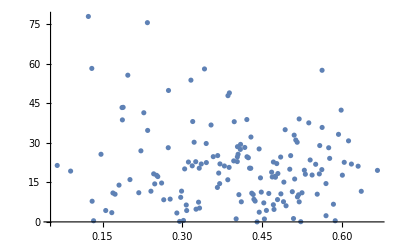

```mathematica
ListPlot[Transpose[{Transpose[tailcontrol1][[13]],absanglecorrect[Transpose[tailcontrol1][[12]]]}],PlotRange->All]
```

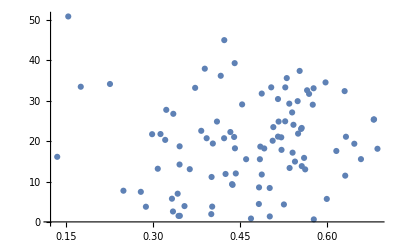

```mathematica
ListPlot[Transpose[{Transpose[tailcontrol2][[32]],absanglecorrect[Transpose[tailcontrol2][[31]]]}],PlotRange->All]
```

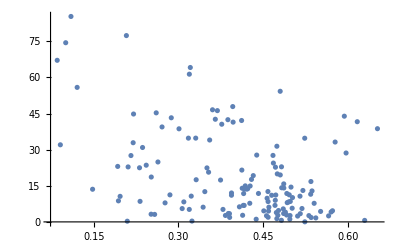

```mathematica
ListPlot[Transpose[{Transpose[tailtsa1][[13]],absanglecorrect[Transpose[tailtsa1][[12]]]}],PlotRange->All]
```

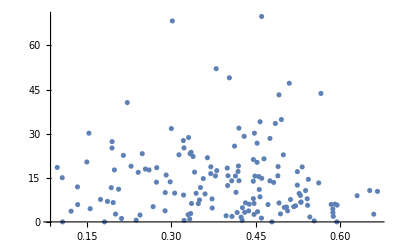

```mathematica
ListPlot[Transpose[{Transpose[tailtsa2][[32]],absanglecorrect[Transpose[tailtsa2][[31]]]}],PlotRange->All]
```

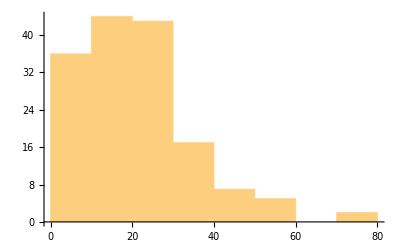

```mathematica
Histogram[absanglecorrect[Transpose[tailcontrol1][[12]]]]
```

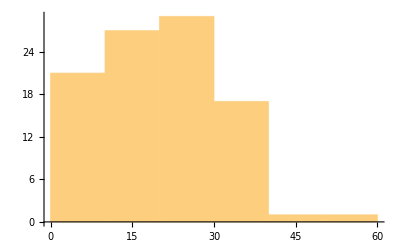

```mathematica
Histogram[absanglecorrect[Transpose[tailcontrol2][[31]]]]
```

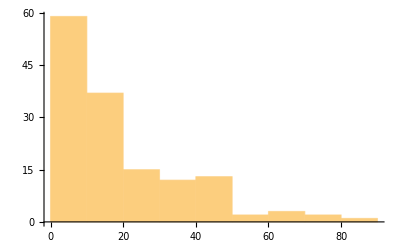

```mathematica
Histogram[absanglecorrect[Transpose[tailtsa1][[12]]]]
```

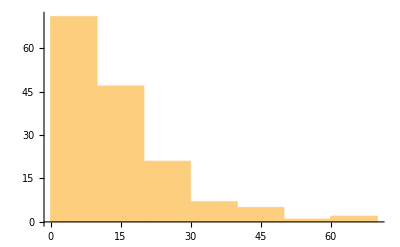

```mathematica
Histogram[absanglecorrect[Transpose[tailtsa2][[31]]]]
```

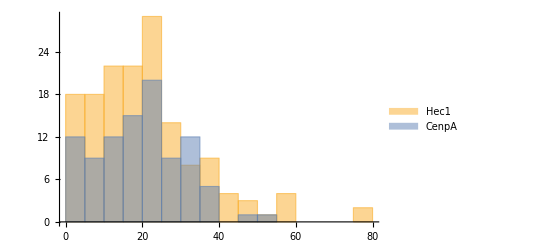

```mathematica
Histogram[{absanglecorrect[Transpose[tailcontrol1][[12]]],absanglecorrect[Transpose[tailcontrol2][[31]]]},20,PlotRange->All,ChartLegends->{Hec1, CenpA}]
```

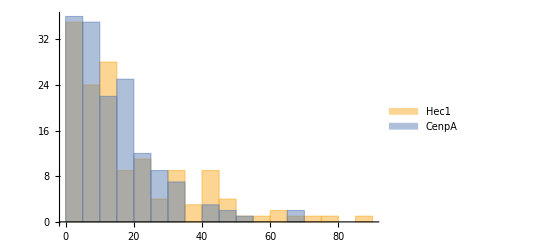

```mathematica
Histogram[{absanglecorrect[Transpose[tailtsa1][[12]]],absanglecorrect[Transpose[tailtsa2][[31]]]},20,PlotRange->All,ChartLegends->{Hec1, CenpA}]
```

```mathematica
Length[controlXY]
```

2444

```mathematica
Length[tsaXY]
```

3049

```mathematica
Length[tailcontrol1]
```

```mathematica
Length[tailcontrol2]
```

```mathematica
Length[tailtsa1]
```

```mathematica
Length[tailtsa2]
```